```mathematica
NormalizeData[symbol_,start_,end_]:=Normal@FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
FinancialChart[symbols_,start_,end_,weightList_:Nothing]:=Module[{lists,allDates,ruleLists,listsWithMissing,mean,weighted,data,table,ts,headings},
lists=NormalizeData[#,start,end]&/@symbols;
allDates=Table[#1&@@i,{stock,lists},{i,stock}]//Fold[Union,#]&;
ruleLists=Table[#1->#2&@@i,{stock,lists},{i,stock}];
listsWithMissing=Table[Module[{association},
association=Association@a;
Table[k->association[k],{k,allDates}]],{a,ruleLists}];
mean=If[Length@symbols>1,Normal@Merge[listsWithMissing,Mean],Nothing];
weighted=If[TrueQ[weightList==Nothing],Nothing,Normal@Merge[listsWithMissing,Total[#*weightList]&]];
data=listsWithMissing~Join~{mean,weighted};
table=Table[Select[Values@d,NumberQ]//{Last@#,StandardDeviation@#}&//{#1,#2,#1/#2}&@@#&,{d,data}];
ts=Transpose@{Keys@#,Values@#}&/@data;
headings=symbols~Join~{If[Length@symbols>1,"Mean",Nothing],If[TrueQ[weightList==Nothing],Nothing,"Weighted Mean"]};
TableForm@{DateListPlot[ts,PlotLegends->headings,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],TableForm[table,TableHeadings->{headings,{"Return","Standard Deviation","Return/SD"}}]}
]
```

{{AAPL,MSFT,AMZN,JNJ,UNH,NVDA,NFLX,INTC,ADBE,GOOG},{5.41576,5.07878,4.79136,4.49928,4.08192,3.88357,3.78018,3.20528,2.91242,2.69713}}

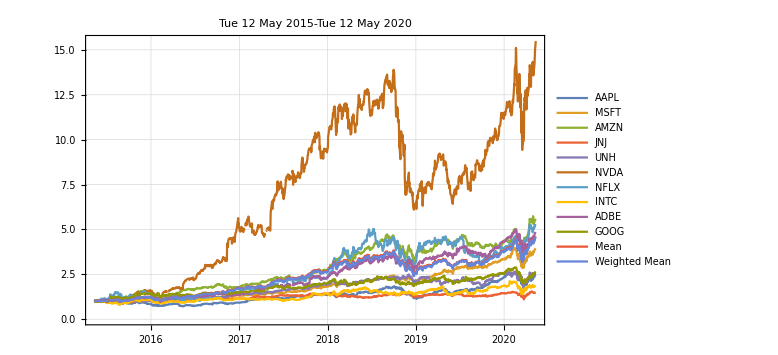
-Graphics-
 | Return | Standard Deviation | Return/SD
AAPL | 2.50276 | 0.441656 | 5.66676
MSFT | 3.94382 | 0.787348 | 5.00899
AMZN | 5.58907 | 1.25515 | 4.45291
JNJ | 1.48412 | 0.14856 | 9.9901
UNH | 2.51823 | 0.506645 | 4.97041
NVDA | 15.4882 | 4.02838 | 3.84478
NFLX | 5.28347 | 1.31272 | 4.02483
INTC | 1.8645 | 0.299984 | 6.21533
ADBE | 4.85073 | 1.13579 | 4.27078
GOOG | 2.65246 | 0.438321 | 6.05142
Mean | 4.61774 | 0.987515 | 4.67612
Weighted Mean | 4.57793 | 0.9726 | 4.7069

```mathematica
{symbols,weights}=ImportString[StringDrop[Import["https://www.ishares.com/us/products/251614/ishares-msci-usa-momentum-factor-etf/1467271812596.ajax?tab=top&fileType=json","String"],3],"JSON"]//Transpose@Table[{i[[1]],i[[6,2,2]]},{i,#[[1,2]]}]&
weights=weights/Total@weights;
start=DatePlus[Today,-Quantity[5, "Years"]];
end=Today;
topChart=FinancialChart[symbols,start,end,weights]
Export[FileNameJoin[{NotebookDirectory[],"topChart.svg"}],topChart];
```

```mathematica
PortfolioChart[stocks_,start_,end_]:=Module[{s,mean,data,symbols,std,return},
s=NormalizeData[#,start,end]&/@stocks;
mean=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{mean};
symbols=stocks~Join~{"mean"};
std=StandardDeviation@mean[[All,2]];
return=Last@mean[[All,2]];
TableForm@{DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All,PlotLabel->DateString@start<>"-"<>DateString@end],{return,std,return/std}//TableForm[#,TableHeadings->{{"Return","SD","Return/SD"},Automatic}]&}
]
```

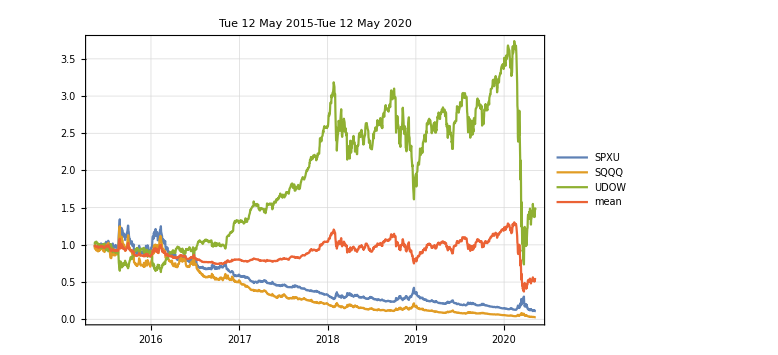
-Graphics-
Return | 0.536266
SD | 0.142552
Return/SD | 3.76191

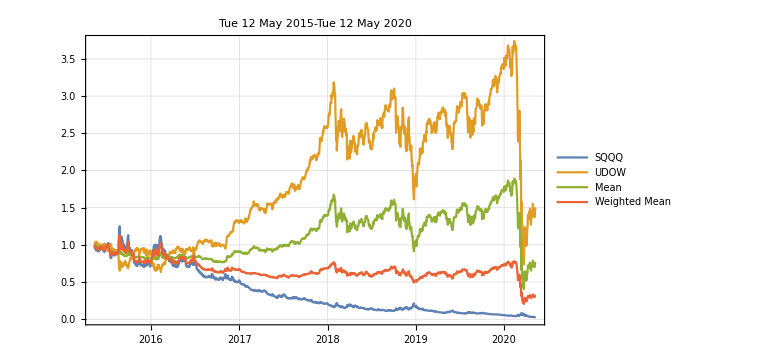
-Graphics-
 | Return | Standard Deviation | Return/SD
SQQQ | 0.02605 | 0.310909 | 0.0837868
UDOW | 1.47301 | 0.834846 | 1.76441
Mean | 0.74953 | 0.294139 | 2.54821
Weighted Mean | 0.315442 | 0.134663 | 2.34246

```mathematica
start2=DatePlus[Today,-Quantity[5, "Years"]];
PortfolioChart[{"SPXU","SQQQ","UDOW"},start2,end]
chart2=FinancialChart[{"SQQQ","UDOW"},start2,end,{0.8,0.2}]
Export[FileNameJoin[{NotebookDirectory[],"chart2.svg"}],chart2];
```